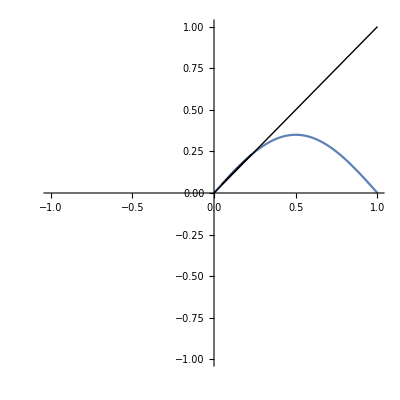

General::munfl: 0.001 7.02452×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.002 1.38463×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.003 2.03832×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

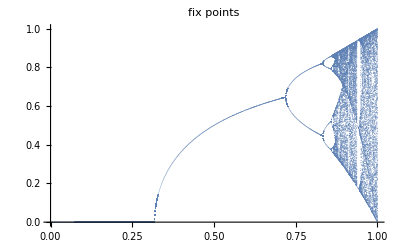

```mathematica
Clear["`*"]
(* This program solves the logistic map. It is a non-linear problem, note -x^2 on next line, and RSolve can not be used.
Instead Nest and NestList are used *)
 (* another way to clear parameter a. 0<a<4. The really interesting region is between 3 and 4*)
g[x_]:= a Sin[ Pi x];
a=0.35;

start=0.05;iter=30;
points=NestList[g,start,iter-1];
lines[x_]:=Line[{{x,x},{x,g[x]},{g[x],g[x]}}];
listlines=lines/@ points;

Plot[ g[x],{x,0,1},
AspectRatio->Automatic,
PlotRange->{{-1,1},{-1,1}},
Epilog->{Line[{{0,0},{1,1}}],listlines}]
(* Below follows commands that generate the bifurcation diagram in the interesting region 3<a<4.  *)
nstart=500;number=128;
(* It works like this I think: after 500 iterations the program takes a look at the following 128
iterations. Union takes away doublets etc. Left is the stable periodic orbit. In the region from
a=3.6 to 4 there is a lot of chaos, that is no stable periodic orbit at all. But in some places
there is a "window". A sign of a short stable periodic orbit *)
afixpoint:=
Union[
Map[
{a,#}&,
NestList[g,Nest[g,start,nstart],number-1]
]
];
amin=0.;amax=1.;step=0.001;
fixpoints=Flatten[Table[afixpoint,{a,amin,amax,step}],1];
ListPlot[ fixpoints,
PlotLabel->"fix points",
PlotRange->{{0,1},{0,1}},
PlotStyle->PointSize[0.001]]
```